```mathematica
S[x_,m_]:=N[Sum[1/(Abs[j*x-Round[j*x]]),{j,1,m}]]
```

```mathematica
T[x_,m_]:=N[Sum[Abs[Csc[j*x]],{j,1,m}]]
```

```mathematica
S[Sqrt[2],20000]
```

431598.

```mathematica
T[Sqrt[2],20000]
```

136899.

```mathematica
S[E,20000]
```

585619.

```mathematica
T[E,20000]
```

132540.

```mathematica
S[GoldenRatio,20000]
```

423228.

```mathematica
T[GoldenRatio,20000]
```

131473.

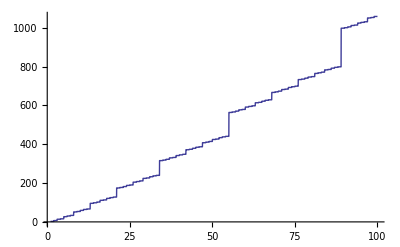

```mathematica
Plot[S[GoldenRatio,m],{m,1,100}]
```

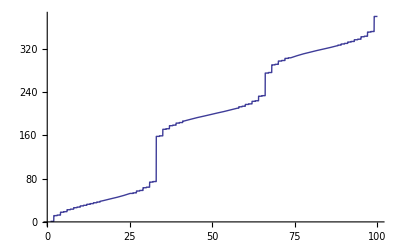

```mathematica
Plot[T[GoldenRatio,m],{m,1,100}]
```

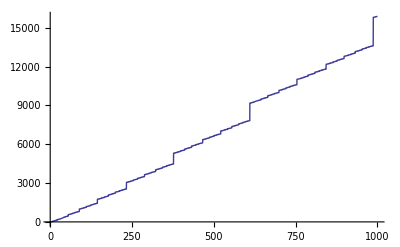

```mathematica
Plot[S[GoldenRatio,m],{m,1,1000}]
```

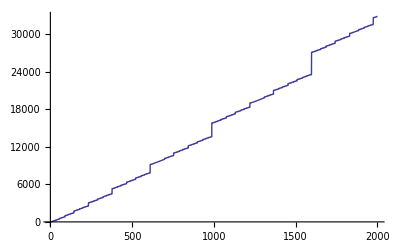

```mathematica
Plot[S[GoldenRatio,m],{m,1,2000}]
```

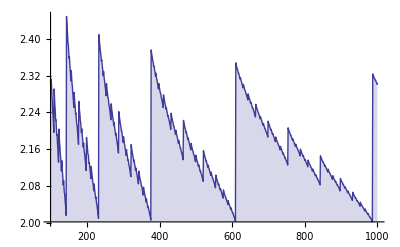

```mathematica
DiscretePlot[S[GoldenRatio,m]/(m*Log[m]),{m,100,1000}]
```

```mathematica
t=Table[S[GoldenRatio,m]/(m*Log[m]),{m,100,1000}];
```

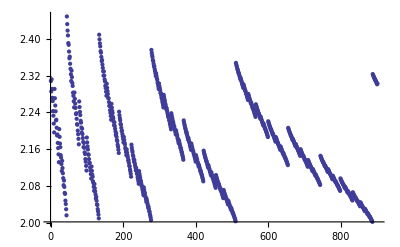

```mathematica
ListPlot[t]
```

```mathematica
ListLinePlot[t]
```

ListLinePlot::lpn: t is not a list of numbers or pairs of numbers.

ListLinePlot[t]

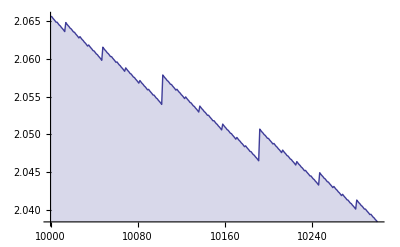

```mathematica
DiscretePlot[S[GoldenRatio,m]/(m*Log[m]),{m,10000,10300}]
```

```mathematica
t1=Table[S[GoldenRatio,m]/(m*Log[m]),{m,1000,5000}];
```

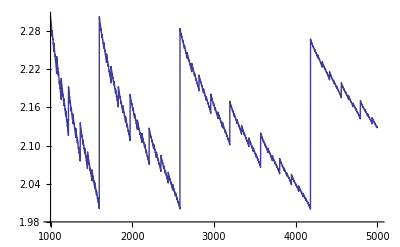

```mathematica
ListLinePlot[t1,PlotRange->Full,DataRange->{1000,5000}]
```

```mathematica
Export["1000-5000.pdf",%19,"PDF"]
```

1000-5000.pdf

```mathematica
t3=Table[S[GoldenRatio,m]/(m*Log[m]),{m,5000,10000}];
```

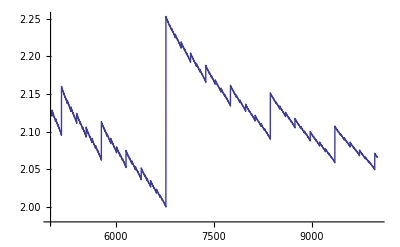

```mathematica
ListLinePlot[t3,DataRange->{5000,10000},PlotRange->Full]
```

```mathematica
Export["5000-10000.pdf",%17,"PDF"]
```

5000-10000.pdf

```mathematica
t4=Table[S[GoldenRatio,m]/(m*Log[m]),{m,20000,25000}];
```

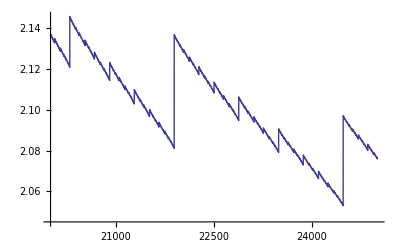

```mathematica
ListLinePlot[t4,DataRange->{20000,25000},PlotRange->Full]
```

```mathematica
Export["20000-25000.pdf",%16,"PDF"]
```

20000-25000.pdf

```mathematica
t5=Table[S[Pi,m]/(m*Log[m]),{m,20000,25000}];
```

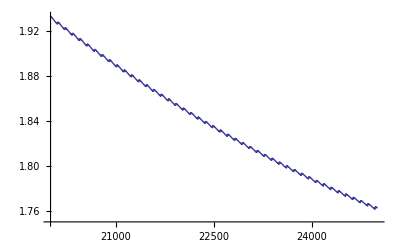

```mathematica
ListLinePlot[t5,DataRange->{20000,25000},PlotRange->Full]
```

```mathematica
Export["pi20000",%22,"PDF"]
```

pi20000

```mathematica
t6=Table[S[EulerGamma,m]/(m*Log[m]),{m,20000,25000}];
```

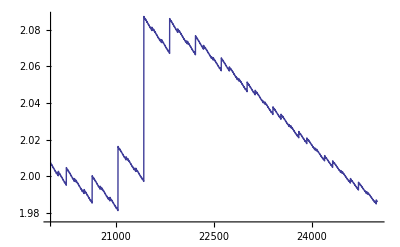

```mathematica
ListLinePlot[t6,DataRange->{20000,25000},PlotRange->Full]
```

```mathematica
Zeta[3.0]
```

1.20206

```mathematica
Apart[1/(x^3(x+1))]
```

1/x^3-1/x^2+1/x-1/(1+x)

```mathematica
Expand[n^2-n-(x+1)^2-(x+1)*(x+n+1)]
```

-2-2 n+n^2-4 x-n x-2 x^2